```mathematica
spring - damper system that takes moving average of sample times.
```

Note. We give the received time values the name ' xin' to avoid confusion with actual system time t. The filter ouptut is called 'x'.

There is noise on the wrap time found in the USB packets. The job here is to filter out the noise

### sample times. Each time is time wrap was reported. grep notifyWrap /var/log/system.log | awk ' // { print $7 "," }'

```mathematica
xin={77247922697324,77248050695066,77248178706058,77248306695626,77248434709995,77248562709897,77248690695529,77248818698454,77248946714719,77249074692265,77249202714728,77249330692925,77249458696330,77249586714109,77249714697843,77249842693815,77249970714215,77250098720433,77250226716710,77250354710225,77250482697901,77250610695552,77250738698336,77250866695883,77250994704101,77251122691160,77251250698405,77251378691126,77251506731437,77251634695203,77251762722647,77251890695541,77252018693310,77252146695531,77252274698171,77252402695108,77252530705102,77252658693737,77252786690950,77252914697996,77253042704734,77253170709808,77253299729872,77253427696358,77253555714645,77253683695692,77253811698286,77253939722048,77254067709316,77254195695635,77254323710045,77254451713608,77254579695735,77254707713957,77254835696159,77254963704003,77255091695477,77255219712958,77255347695576,77255475695822,77255603715025,77255731710071,77255859696266,77255987705028,77256115695974,77256243695925,77256371696617,77256499709610,77256627705623,77256755709835,77256883695763,77257011695927,77257139695829,77257267697582,77257395691134,77257523695761,77257651695416,77257779698106,77257907697838,77258035724046,77258163695901,77258291714508,77258419709970,77258547696321,77258675710293,77258803709869,77258931697735,77259059695704,77259187696240,77259315698603,77259443696569,77259571697730,77259699697883,77259827714543,77259955698108,77260083695419,77260211695356,77260339715962,77260467710122,77260595698203,77260723695559,77260851697972,77260979697954,77261107709739,77261235722124,77261363710036,77261491714656,77261619695742,77261747705280,77261875695853,77262003698136,77262131695470,77262259698467,77262387695767,77262515708716,77262643695234,77262771695491,77262899695663,77263027713342,77263155695691,77263283698268,77263411710223,77263539711234,77263667695496,77263795731067,77263923710753,77264051695965,77264179690714,77264307697819,77264435711548,77264563712944,77264691698472,77264819714273,77264947695672,77265075714896,77265203698024,77265331695635,77265459695818,77265587697815,77265715696008,77265843697985,77265971695625,77266099713259,77266227696130,77266355696202,77266483714649,77266611691896,77266739714683,77266867695076,77266995716752,77267123696708,77267251766768,77267379695398,77267507704079,77267635695763,77267763697626,77267891696056,77268019695721,77268147697863,77268275718152,77268403697927,77268531714668,77268659697856,77268787729020,77268915695474,77269043698153,77269171696090,77269299697872,77269427696197,77269555697871,77269683695797,77269811698316,77269939695927,77270067714307,77270195695833,77270323696829,77270451695506,77270579698549,77270707696791,77270835715312,77270963714753,77271091709695,77271219695439,77271347695415,77271475701076,77271603696343,77271731695837,77271859703853,77271987698458,77272115695912,77272243708999,77272371727201,77272499698531,77272627715853,77272755724997,77272883693225,77273011695494,77273139695854,77273267700760,77273395714528,77273523700328,77273651695601,77273779717091,77273907696431,77274035699554,77274163695971,77274291698230,77274419698232,77274547697944,77274675714459,77274803715835,77274931710239,77275059725306,77275187714899,77275315697967,77275443697804,77275571714765,77275699695304,77275827704681,77275955698604,77276083703763,77276211695861,77276339726479,77276467709839,77276595691240,77276723692808,77276851695174,77276979691115,77277107696227,77277235695434,77277363695735,77277491695040,77277619716337,77277747695665,77277875698019,77278003709865,77278131720180,77278259696148,77278387695941,77278515694636,77278643698086,77278771698210,77278899695489,77279027691540,77279155714604,77279283695613,77279411698982,77279539696109,77279667698194,77279795695188,77279923695791,77280051696642,77280179697927,77280307695644,77280435697057,77280563695966,77280691698457,77280819706573,77280947713641,77281075696026,77281203695402,77281332709783,77281460696612,77281588695764,77281716695785,77281844714257,77281972731231,77282100712983,77282228714298,77282356695789,77282484690700,77282612695509,77282740725954,77282868738220,77282996709430,77283124715285,77283252699110,77283380710249,77283508697997,77283636717539,77283764710228,77283892697858,77284020698762,77284148703034,77284276695675,77284404697626,77284532713270,77284660698252,77284788695955,77284916728947,77285044695743,77285172698175,77285300695731,77285428713951,77285556696158,77285684713158,77285812714944,77285940692413,77286068715580,77286196695947,77286324698881,77286452695893,77286580696984,77286708711512,77286836715045,77286964696904,77287092696693,77287220712872,77287348714830,77287476715037,77287604699243,77287732696228,77287860695934,77287988696156,77288116715286,77288244709452,77288372695865,77288500698947,77288628698287,77288756704900,77288884710210,77289012695566,77289140715591,77289268698128,77289396718226,77289524695497,77289652714397,77289780696928,77289908731036,77290036695778,77290164705922,77290292709958,77290420695951,77290548695311,77290676698913,77290804696509,77290932709637,77291060697381,77291188710999,77291316697891,77291444715554,77291572699742,77291700690580,77291828710178,77291956704432,77292084724272,77292212712961,77292340714622,77292468695774,77292596696228,77292724710248,77292852710296,77292980695393,77293108696288,77293236714206,77293364695908,77293492698108,77293620730570,77293748707173,77293876714236,77294004709277,77294132704370,77294260711815,77294388698779,77294516698024,77294644720163,77294772698194,77294900698662,77295028714411,77295156704690,77295284694078,77295412695671,77295540701812,77295668714933,77295796698402,77295924715598,77296052714207,77296180714776,77296308696517,77296436698435,77296564696390,77296692697409,77296820695515,77296948710190,77297076696413,77297204696142,77297332696187,77297460691377,77297588697695,77297716699576,77297844695946,77297972697726,77298100690797,77298228697845,77298356698304,77298484717399,77298612695389,77298740714387,77298868695494,77298996710827,77299124696254,77299252696498,77299380695959,77299508695780,77299636695123,77299764710079,77299892695704,77300020697790,77300148696301,77300276714253,77300404691870,77300532705325,77300660725645,77300788714191,77300916716293,77301044715473,77301172691124,77301300731422,77301428698405,77301556698222,77301684695741,77301812697644,77301940714646,77302068698380,77302196696716,77302324696040,77302452695916,77302580694991,77302708695622,77302836708983,77302964698145,77303092714680,77303220696196,77303348697575,77303476695708,77303604714398,77303732695284,77303860714913,77303988695297,77304116714692,77304244695580,77304372706927,77304500695794,77304628714400,77304756696447,77304884698608,77305012695723,77305140714604,77305268716435,77305396699729,77305524711287,77305652696125,77305780697550,77305908697648,77306036709341,77306164722688,77306292713220,77306420714695,77306548722506,77306676714088,77306804697793,77306932714298,77307060707354,77307188698506,77307316691133,77307444727572,77307572696205,77307700693733,77307828716272,77307956726492,77308084709804,77308212714169,77308340715614,77308468695162,77308596698434,77308724695741,77308852695972,77308981696974,77309109696815,77309237692717,77309365700290,77309493688574,77309621699483,77309749696837,77309877714028,77310005697358,77310133699561,77310261712644,77310389715422,77310517693678,77310645705623,77310773699276,77310901714960,77311029698985,77311157711328,77311285697089,77311413701236,77311541693846,77311669708678,77311797699403,77311925700107,77312053697408,77312181699400,77312309717053,77312437706861,77312565711222,77312693699027,77312821717442,77312949698490,77313077712383,77313205698585,77313333717140,77313461699672,77313589702532,77313717696887,77313845724332,77313973699345,77314101716020,77314229697647,77314357697034,77314485696564,77314613699671,77314741692382,77314869697197,77314997697173,77315125705674,77315253696909,77315381715565,77315509699581,77315637716030,77315765710933,77315893699211,77316021723533,77316149710505,77316277699253,77316405715367,77316533714139,77316661715978,77316789717478,77316917697688,77317045698704,77317173700094,77317301706720,77317429699096,77317557699188,77317685700594,77317813699228,77317941694915,77318069693960,77318197696551,77318325699557,77318453697074,77318581734908,77318709699448,77318837698994,77318965696424,77319093699084,77319221696922,77319349715591,77319477707803,77319605715475,77319733692820,77319861715394,77319989698677,77320117730939,77320245715531,77320373714145,77320501700370,77320629715687,77320757719829,77320885715526,77321013697087,77321141697332,77321269732619,77321397715369,77321525696750,77321653697160,77321781689722,77321909718741,77322037697317,77322165696818,77322293696910,77322421699094,77322549696649,77322677699158,77322805696648,77322933696773,77323061732041,77323189699297,77323317696760,77323445715148,77323573698722,77323701701044,77323829698207,77323957717151,77324085711415,77324213696993,77324341699562,77324469730069,77324597696953,77324725696974,77324853692793,77324981714103,77325109713709,77325237711211,77325365697325,77325493697002,77325621697292,77325749713011,77325877715503,77326005699198,77326133697360,77326261699709,77326389697006,77326517712841,77326645692082,77326773699201,77326901713864,77327029715408,77327157699604,77327285715237,77327413697528,77327541715487,77327669711106,77327797697517,77327925688221,77328053711557,77328181696856,77328309711010,77328437696767,77328565705922,77328693696871,77328821699225,77328949696931,77329077720298,77329205697131,77329333710839,77329461699582,77329589693961,77329717699290,77329845699683,77329973694883,77330101699106,77330229696432,77330357699842,77330485718495,77330613699225,77330741715590,77330869699425,77330997699432,77331125696836,77331253711090,77331381736636,77331509718534,77331637697258,77331765696710,77331893699462,77332021697224,77332149716019,77332277716107,77332405696699,77332533699678,77332661696577,77332789697472,77332917699328,77333045708562,77333173696839,77333301696574,77333429697576,77333557709948,77333685696547,77333813694607,77333941694404,77334069705657,77334197697180,77334325715529,77334453707395,77334581700539,77334709696930,77334837734071,77334965731447,77335093699349,77335221700600,77335349699602,77335477714646,77335605715746,77335733699540,77335861711130,77335989717276,77336117688595,77336245711782,77336373730763,77336501715485,77336630698803,77336758704077,77336886720082,77337014698198,77337142695811,77337270716516,77337398716126,77337526716008,77337654696300,77337782695778,77337910705517,77338038716678,77338166714530,77338294714352,77338422695507,77338550690858,77338678714122,77338806697707,77338934696037,77339062695997,77339190698279,77339318695708,77339446713976,77339574696181,77339702714465,77339830707947,77339958695861,77340086714787,77340214715200,77340342703695,77340470696045,77340598698343,77340726723042,77340854698522,77340982696050,77341110709964,77341238727560,77341366695804,77341494714966,77341622728018,77341750709581,77341878695617,77342006714544,77342134736295,77342262698561,77342390710361,77342518695265,77342646698602,77342774714802,77342902695863,77343030693938,77343158696204,77343286698077,77343414724312,77343542714353,77343670685462,77343798700805,77343926697675,77344054695449,77344182695844,77344310710197,77344438696325,77344566706067,77344694704168,77344822698949,77344950698997,77345078722142,77345206714517,77345334710313,77345462717442,77345590734860,77345718715141,77345846714617,77345974730342,77346102698234,77346230710127,77346358714631,77346486698260,77346614714801,77346742714527,77346870695964,77346998697893,77347126695920,77347254714024,77347382714367,77347510714840,77347638695656,77347766695792,77347894697958,77348022698621,77348150698212,77348278695345,77348406697611,77348534695466,77348662698387,77348790696176,77348918698892,77349046695616,77349174695892,77349302695463,77349430708427,77349558695609,77349686715724,77349814695991,77349942697576,77350070698049,77350198695620,77350326695503,77350454714674,77350582695798,77350710714448,77350838713030,77350966698505,77351094695867,77351222695933,77351350695478,77351478697997,77351606695876,77351734690907,77351862698019,77351990710199,77352118721060,77352246715876,77352374695709,77352502695727,77352630694107,77352758697978,77352886698802,77353014731422,77353142715099,77353270711813,77353398696050,77353526715201,77353654729702,77353782715486,77353910714421,77354038711781,77354166730467,77354294698595,77354422695298,77354550698559,77354678715942,77354806698042,77354934694733,77355062695790,77355190725575,77355318714394,77355446695788,77355574732089,77355702709218,77355830716609,77355958698949,77356086726591,77356214698086,77356342698183,77356470726611,77356598695412,77356726714793,77356854695557,77356982714572,77357110696606,77357238710600,77357366718953,77357494716439,77357622695613,77357750714825,77357878696926,77358006696430,77358134695446,77358262714398,77358390696102,77358518709096,77358646696024,77358774714727,77358902691635,77359030711894,77359158695386,77359286712370,77359414716817,77359542710429,77359670698083,77359798710112,77359926714861,77360054693284,77360182691865,77360310695547,77360438695236,77360566698128,77360694695606,77360822730838,77360950695563,77361078695765,77361206695991,77361334691471,77361462695735,77361590714498,77361718710131,77361846731912,77361974696621,77362102698194,77362230717811,77362358704994,77362486691804,77362614696579,77362742695746,77362870697440,77362998698579,77363126698653,77363254714911,77363382715029,77363510695972,77363638733446,77363766695905,77363894698404,77364022696148,77364150714916,77364279714031,77364407698237,77364535710239,77364663695773,77364791717137,77364919699493,77365047701778,77365175695630,77365303698071,77365431696418,77365559710509,77365687696156,77365815698435,77365943706087,77366071714742,77366199695511,77366327721693,77366455695997,77366583714741,77366711695923,77366839696059,77366967716782,77367095698096,77367223696463,77367351696022,77367479698623,77367607698871,77367735695838,77367863698023,77367991698231,77368119714621,77368247698195,77368375698242,77368503696094,77368631699449,77368759709857,77368887690890,77369015696930,77369143703958,77369271691212,77369399714697};
```

```mathematica
xin=Drop[xin,-20]; (*end is always a mess *)
```

96 kHz
outputSize= 586 multFactor= 6
new bufferSize = 73728 numSamplesInBuffer = 12288

```mathematica
bufsize=12288;
```

```mathematica
rate=96000;
```

#### Expected time between wraps in ns

```mathematica
Texpected=10^9 bufsize /rate
```

128000000

## CHECK We may want to skip the first frames is this is happening consistently

#### If we start at the wrong moment, where the timing is off from the main pulse, the filter has to adjust to get into the beat. Apparently the first beats are off the main beat. This makes huge difference in max error/drift after fitlering.

```mathematica
xin=Drop[xin,5]; (* test. There seems a hickup in sample 3 *)
```

```mathematica
deltas=10^-6(Drop[xin,1]-Drop[xin,-1]);
```

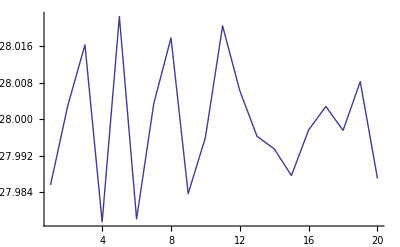

```mathematica
ListPlot[Take[deltas,20],PlotJoined->True,PlotRange->All]
```

```mathematica
(*xin=Take[xin,{200,220}]; (*testing *)
```

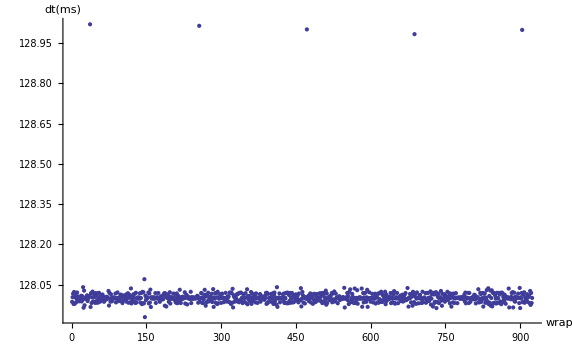

```mathematica
ListPlot[deltas, AxesLabel->{"wrap","dt(ms)"},PlotRange->All]
```

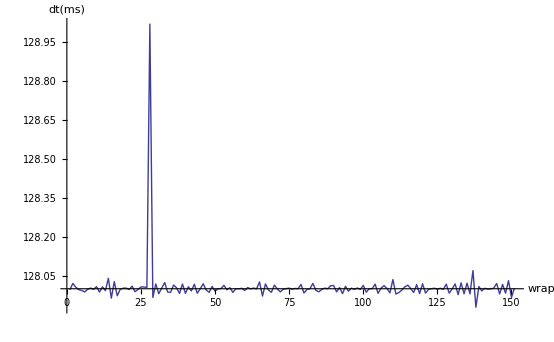

```mathematica
ListPlot[Take[deltas,{10,160}], AxesLabel->{"wrap","dt(ms)"},PlotRange->All,PlotJoined->True]
```

```mathematica
estimated=Mean[10^-6(Drop[xin,1]-Drop[xin,-1])]//N
```

128.005

```mathematica
NumMeas=10;
```

```mathematica
estimated1=(Plus@@Take[deltas,NumMeas]+1)/NumMeas//N
```

128.098

Is it close?

```mathematica
(Texpected-10^6 estimated)/Texpected
```

-0.0000421584

#### Init the filter with first sample

```mathematica
x0=xin[[1]]
```

77248562709897

```mathematica
xin=Drop[xin,1]; (* first element was used so do not reuse *)
```

```mathematica
x=x0; (* filtered x *)
u=0; (* u = x-xin : the 'error' is the spring extension *)
dx=Texpected; (* dx/dt = expected change rate of filtered x *)
```

```mathematica
dx=10^6 estimated1
```

1.28098×10^8

```mathematica
xin[[1]]-x
```

127985632

#### Spring constant

```mathematica
K=1;
```

Damping constant

The mass, this determines how slow system follows changes in xin. Bigger=slower.

```mathematica
M=10000;
```

```mathematica
Da=2 √(M K); (*cricital damping *)
```

## Filter

#### Simple filter. This does work in the right direction but lacks damping so lot of overshoot.

```mathematica
filter[inputx_]:=Module[{},
xnext=x+dx;
du=inputx-x;
dx=(99dx+du)/100; (*exponential towards target *)
x=xnext;
x
]
```

#### spring - damper based filter. Is jumpy.

```mathematica
filter[inputx_]:=Module[{},(*{F,du,xnext,unext},*)
xnext=x+dx ;(* the next filtered output *)
unext=inputx-xnext; (*error u *)

du = unext-u; (* change of the error, for damping *)
F=K unext + Da du; (* force on spring *)
dx = dx + F/M ; 

x=xnext; u=unext; (* update the filter *)
x
];
```

#### spring - damper filter with outlier check/skip

Works great for the test set. Only worry is that the jitter detect uses the du which is change of error.
  An absolute distance of unext from Texpected might be better but in practice it seems worse

```mathematica
filter[inputx_]:=Module[{xnext, unext, du, F},(*{F,du,xnext,unext},*)
xnext=x+dx ;(* the next filtered output *)
unext=inputx-xnext; (*error u *)

du = unext-u; (* change of the error, for damping *)
F=K unext + Da du; (* force on spring *)
dx = dx + F/M ;
x=xnext; u=unext; (* update the filter *)
x
];
```

```mathematica
xfiltered = filter/@xin;
```

```mathematica
10^-6(xfiltered-xin)[[4]]
```

0.399043

### Does it follow xin?

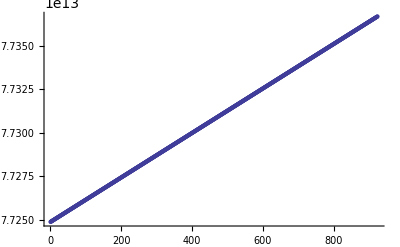

```mathematica
ListPlot[xfiltered]
```

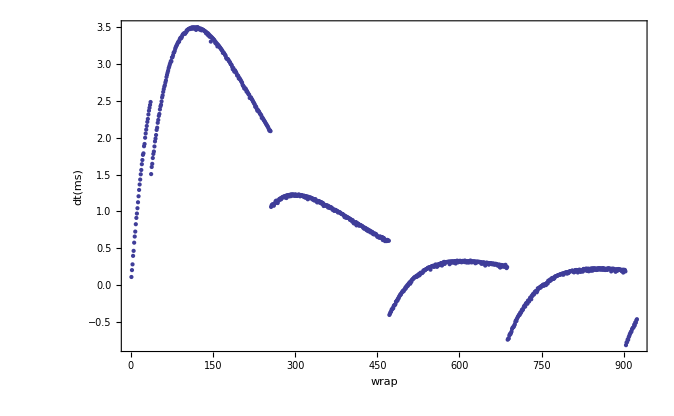

```mathematica
ListPlot[10^-6(xfiltered-xin), FrameLabel->{"wrap","dt(ms)"},PlotRange->All,Frame->True]
```

So the data can come in up to 6 ms late. This is the timestamps straight coming from USB

### Does it keep a solid rate without jumping?

```mathematica
deltas=(Drop[xfiltered,1]-Drop[xfiltered,-1])-Texpected;
```

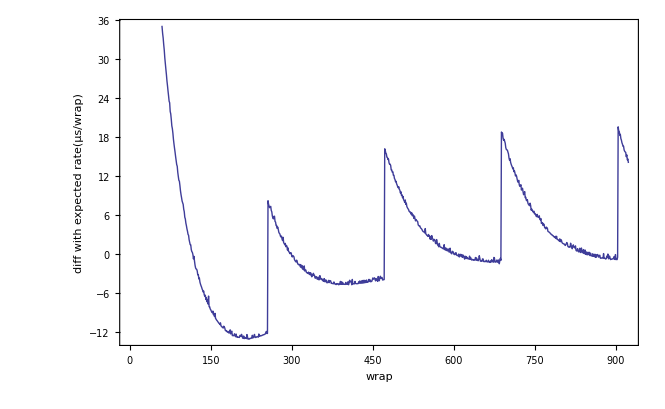

```mathematica
ListPlot[10^-3((Drop[xfiltered,1]-Drop[xfiltered,-1])-Texpected), FrameLabel->{"wrap","diff with expected rate(μs/wrap)"},Frame->True,PlotJoined->True]
```

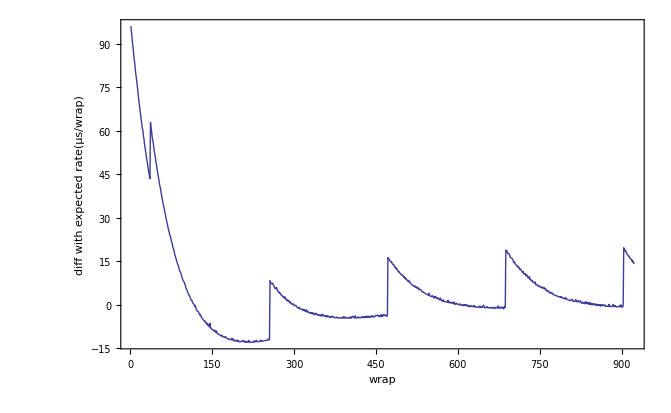

```mathematica
ListPlot[10^-3((Drop[xfiltered,1]-Drop[xfiltered,-1])-Texpected), FrameLabel->{"wrap","diff with expected rate(μs/wrap)"},Frame->True,PlotJoined->True,PlotRange->All]
```